## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`(* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Graph format

```mathematica
includeFrame = True;
imageSize = Medium;
frameStyle = Directive[Black,Thickness[0.003]];
colorlist = ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, vartRes, D[vartRes, t],sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

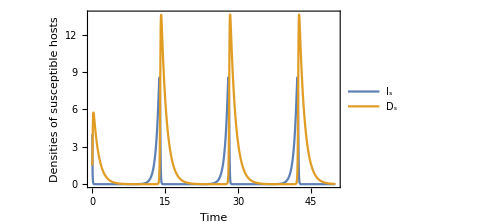
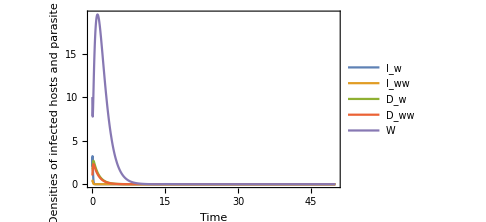
-Graphics- | -Graphics-

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 50;

init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All}, PlotLegends->{"I_s",  "D_s"}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize,Frame->includeFrame,FrameStyle->frameStyle];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, All},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize, Frame-> includeFrame];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

## Bifurcation γ

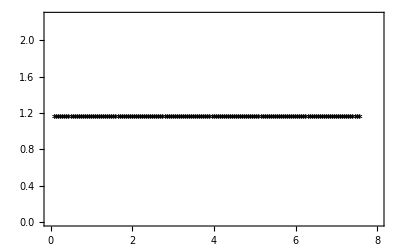

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};
γrange = Range[0.1, 8, 0.05];

solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Pool to intermediate host transmission (γ)", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parγ, γ, γrange, eqγzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

## Bifurcation β_w

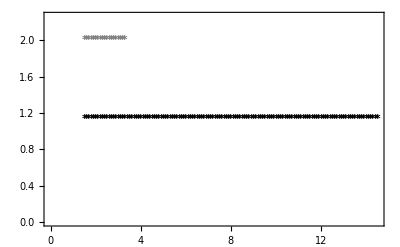

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];

solsβw = NSolve[Thread[(sysfunc0/.parβw/.βw-> 1.5) == 0], varRes];

eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};

eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black, Frame->includeFrame, FrameLabel->{"Intermediate - definitive hosts transmission β_w", "Equilibrium"}, PlotLegends->{"I_s"}];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc0, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray, PlotLegends->{"D_s"}];
Show[p0, p1]
```

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, vartRes,D[vartRes, t], sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

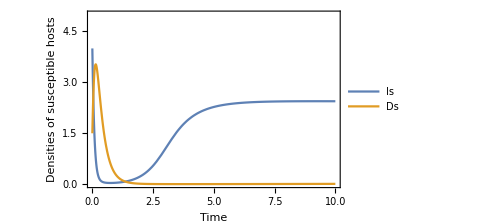
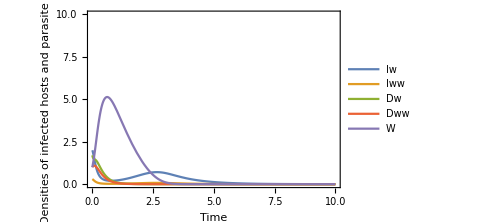
-Graphics- | -Graphics-

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 10;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];

{Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame->includeFrame,FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];

p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

## Disease stable equilibrium

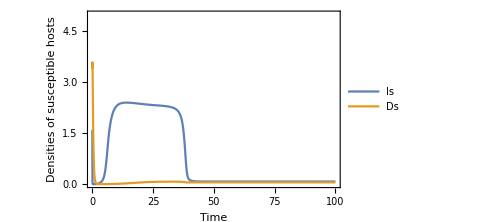
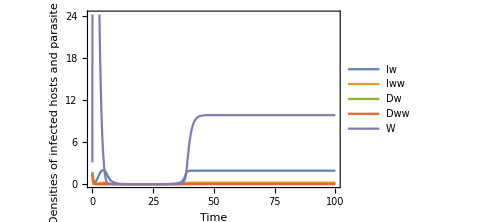
-Graphics- | -Graphics-

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 49, fww-> 49*8.51,δ-> 0.9, k -> 0.26};

condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt = 100;

{Is[0]== 1.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==1.1, W[0] == 3.1};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}, AccuracyGoal->Infinity] ;

solsDS = NSolve[Thread[(sysfunc1/.condsimplifyNL/.prEcoDSNL) == 0], varRes];

p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> includeFrame, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->imageSize];
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolDS], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 24.2}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> includeFrame, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->imageSize];
Grid[{{p1, p2}}]
```

## Bifurcation f_w (f_ww = ϵ f_w)

Calculation

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};
fwrangeFWrd = Range[40.5, 51.5, 0.05];
fwrangeBWrd = Range[40.5, 32, -0.05];
fwrange = Range[32, 51.5, 0.3];

(*Find all solutions of the system with the given parameter values*)
solsfwAll = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw= Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero = Select[solsfwAll, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

eqfwFWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeFWrd, varRes, solsfw];
eqfwBWrd = FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, fwrangeBWrd, varRes, solsfw];

rangeIs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.1, 2}};
rangeDs = {{fwrangeBWrd[[-1]], fwrangeFWrd[[-1]]}, {-0.01, 0.03}};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::reged: The point {2.32041,0.000842335,0.0000935928,0.0759001,0.0000300178,0.,0.000140786} is at the edge of the search region {0.,∞} in coordinate 6 and the computed search direction points outside the region.

Plotting

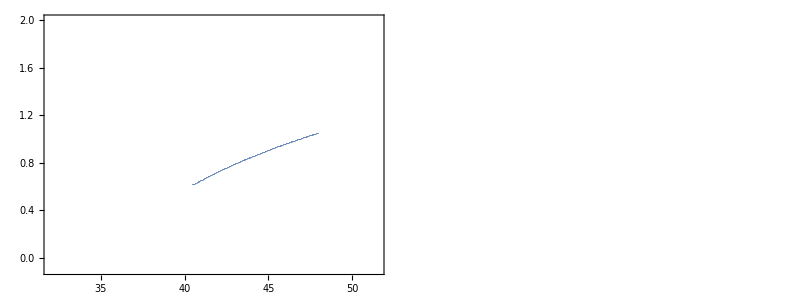

```mathematica
xaxis =fwrangeFWrd[[1;; Length[eqfwFWrd]]];
 {#}& /@Transpose[{xaxis, Iw/.eqfwFWrd}];
p0 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium I_w"}];

{#}& /@Transpose[{xaxis, Dw/.eqfwFWrd}];
p1 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwFWrd], PlotStyle-> colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{"Parasite reproduction in single infection(f_w)", "Equilibrium D_w"}];

xaxis = fwrangeBWrd[[1;;Length[eqfwBWrd]]];
{#}& /@Transpose[{xaxis, Iw/.eqfwBWrd}];
p2 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{xaxis, Dw/.eqfwBWrd}];
p3 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, xaxis, eqfwBWrd], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];


eqfwzero = ConstantArray[solsfwzero, Length[fwrange]];
{#}& /@Transpose[{fwrange, Iw/.eqfwzero}];
p4 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[1]], PlotRange->rangeIs, ImageSize->imageSize];

{#}& /@Transpose[{fwrange, Dw/.eqfwzero}];
p5 = ListPlot[%, PlotMarkers->ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero], PlotStyle->colorlist[[2]], PlotRange->rangeDs, ImageSize->imageSize];

pp0 = Show[p0,  p2, p4];
pp1 = Show[p1, p3, p5];

Grid[{{pp0, pp1}}]
(*Export["bifurcation_fw_NL.jpg", %]*)
```

```mathematica
On[Assert];
rr= Range[35, 37, 0.02];
FollowRoot[sysfunc1/.fww-> ϵ fw, parfw, fw, rr, varRes, solsfwzero];
xx =ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, rr, %];
pos = Position[xx, "*", 1, 1][[1]][[1]];
xx[[pos]] == "*"//Assert
xx[[pos-1]] == "." //Assert
fwbifur = rr[[pos]]
```

35.84

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 1.01;
ϵend = 6;
ϵinterval = 0.5;
fwstart = 35;
fwend = 45;
fwinterval = 1;
```

```mathematica
NSolveCodim2Positive[system_, commonpars_, bifurpar1_, bifurpar2_,bfparsName_, equisymbol_,variables_]:=
Module[
{sys, cpar,bfpar1, bfpar2,  vars, bfpName,eqsym,parspairVal, eqAll, eqpos},
sys = system;
cpar = commonpars;
bfpar1 = bifurpar1;
bfpar2 = bifurpar2;
bfpName = bfparsName;
eqsym = equisymbol;
vars = variables;
eqAll = NSolve[Thread[(sys/.cpar/.bfpar1/. bfpar2)==0], vars, Reals];
eqpos = Select[eqAll,And@@Thread[(vars/.# )> 0]&];
parspairVal = {bfpar1[[1]][[2]], bfpar2[[1]][[2]]};
If[eqpos != {}, Join[{bfpName -> parspairVal}, {eqsym -> eqpos[[1]]}] , Unevaluated@Sequence[]]
]
```

```mathematica
ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}]
```

$Aborted